## Schwarzschild in r_* coordinate

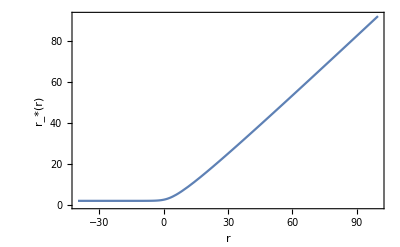

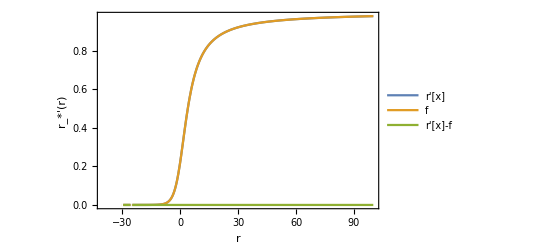

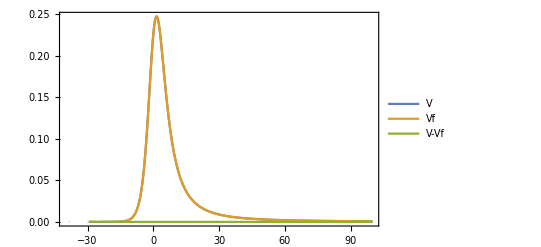

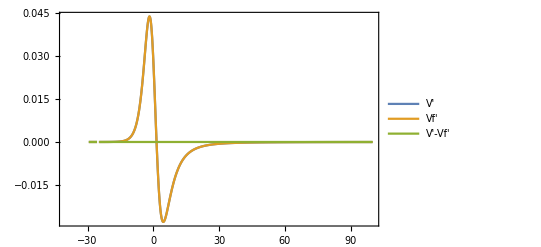

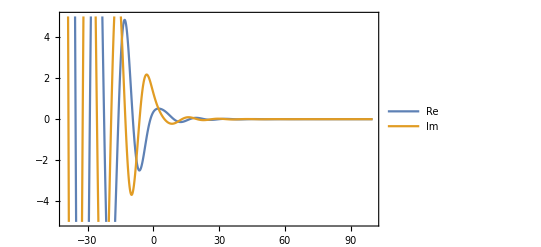

-Graphics3D-

```mathematica
m=1;xi=-40;xf=100;
vlogk0=Table[
vk:=y/.FindRoot[x ==y + 2m Log[y/(2m) - 1], {y,2m+0.0001}];
{x,vk},{x,xi,xf,0.01}];
r=Interpolation[vlogk0];

l=2;β=1 - s^2;s=0;ω=ωr-ⅈ ωi;ωr=0.4832110283763369;ωi=0.09680484660403677;η=((l-1)(l+2))/2;
f[x_]=1 - (2m)/r[x];
Va[x_]=f[x]((l(l+1))/r[x]^2+ (2m β)/r[x]^3);
Vp[x_]=f[x]/(r[x]^3(η r[x]+ 3m)^2)(2 η^2(η+1)r[x]^3+ 6 η^2 m r[x]^2 + 18η m^2 r[x] + 18 m^3);

Plot[r[x],{x,xi,xf},Frame->True,AxesLabel->{"r","r_*(r)"}]
Plot[{r'[x],f[x],r'[x]-f[x]},{x,xi,xf},Frame->True,AxesLabel->{"r","r_*'(r)"},PlotLegends->{"r'[x]","f","r'[x]-f"},PlotRange->Full]

V=Va;

vlogkv=Table[
vk:=N[V[x]];
{x,vk},{x,xi,xf,0.01}];
Vf=Interpolation[%];

Plot[{V[x],Vf[x],V[x]-Vf[x]},{x,xi,xf},Frame->True,PlotLegends->{"V","Vf","V-Vf"},PlotRange->Full]
Plot[{V'[x],Vf'[x],V'[x]-Vf'[x]},{x,xi,xf},Frame->True,PlotLegends->{"V'","Vf'","V'-Vf'"},PlotRange->Full]
(*Plot[f[x],{x,xi,xf},Frame->True]*)

h[x_] =ⅇ^(-ωi r[x])(Cos[ωr r[x]]+ⅈ Sin[ωr r[x]]);

Solution=NDSolve[{ψ''[x] + (ω^2-Vf[x])ψ[x]== 0, ψ[xf]==h[xf],ψ'[xf]==h'[xf]},ψ,{x,xi,xf},MaxSteps->Infinity,MaxStepFraction->0.001];
Plot[{Evaluate[Re[ψ[x]]/.Solution],Evaluate[Im[ψ[x]]/.Solution]},{x,xi,xf},Frame->True,PlotLegends->{"Re","Im"},PlotRange->{{xi,xf},{-5,5}}]
Ψ[x_,t_]=Evaluate[ψ[x]/.Solution] ⅇ^(-ⅈ ω t);
Plot3D[Re[Ψ[x,t]],{x,xf-20,xf},{t,0,20}]
```

## Schwarzschild, Bardeen, Hayward and RN comparison

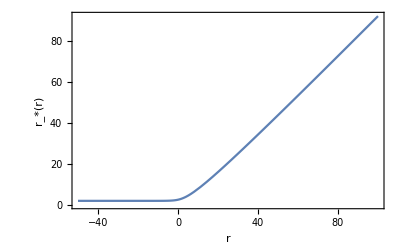

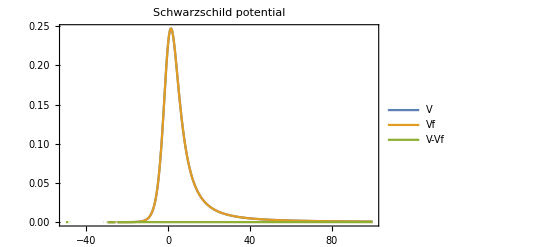

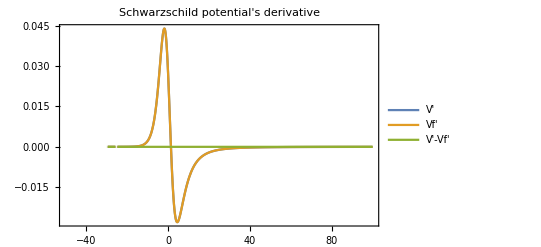

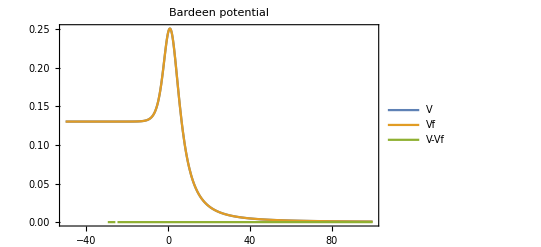

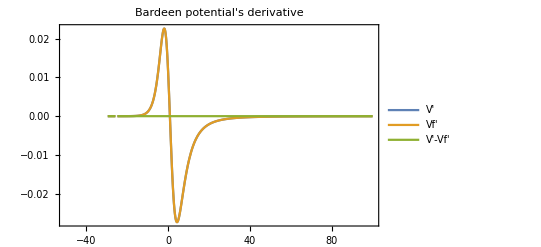

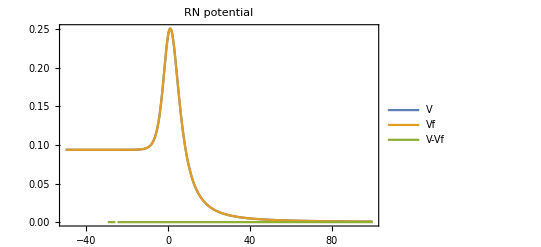

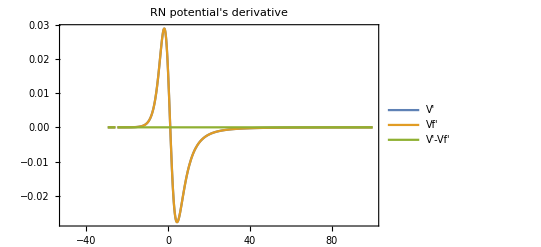

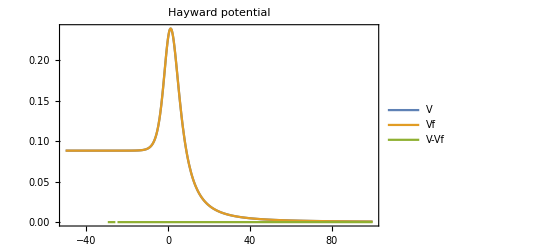

```mathematica
m=1;xi=-50;xf=100;
vlogk0=Table[
vk:=y/.FindRoot[x ==y + 2m Log[y/(2m) - 1], {y,2m+0.0001}];
{x,vk},{x,xi,xf,0.01}];
r=Interpolation[vlogk0];
Plot[r[x],{x,xi,xf},Frame->True,AxesLabel->{"r","r_*(r)"}]

l=2;β=1 - s^2;s=0;ω=ωr-ⅈ ωi;ωr=0.4832110283763369;ωi=0.09680484660403677;η=((l-1)(l+2))/2;
f[x_]=1 - (2m)/r[x];
Va[x_]=f[x]((l(l+1))/r[x]^2+ (2m β)/r[x]^3);
Vp[x_]=f[x]/(r[x]^3(η r[x]+ 3m)^2)(2 η^2(η+1)r[x]^3+ 6 η^2 m r[x]^2 + 18η m^2 r[x] + 18 m^3);

V=Va;

vlogkv=Table[
vk:=N[V[x]];
{x,vk},{x,xi,xf,0.01}];
Vf=Interpolation[%];

h[x_] =ⅇ^(-ωi r[x])(Cos[ωr r[x]]+ⅈ Sin[ωr r[x]]);

Plot[{V[x],Vf[x],V[x]-Vf[x]},{x,xi,xf},Frame->True,PlotLegends->{"V","Vf","V-Vf"},PlotRange->Full,PlotLabel->"Schwarzschild potential"]
Plot[{V'[x],Vf'[x],V'[x]-Vf'[x]},{x,xi,xf},Frame->True,PlotLegends->{"V'","Vf'","V'-Vf'"},PlotRange->Full,PlotLabel->"Schwarzschild potential's derivative"]

Solution=NDSolve[{ψ''[x] + (ω^2-Vf[x])ψ[x]== 0, ψ[xf]==h[xf],ψ'[xf]==h'[xf]},ψ,{x,xi,xf},MaxSteps->Infinity,MaxStepFraction->0.001];
psr=Plot[Evaluate[Re[ψ[x]]/.Solution],{x,xi,xf},Frame->True,PlotStyle->Red,PlotRange->{{xi,xf},{-5,5}},PlotLegends->{"Schwarzschild"}];
psi=Plot[Evaluate[Im[ψ[x]]/.Solution],{x,xi,xf},Frame->True,PlotStyle->Red,PlotRange->{{xi,xf},{-5,5}},PlotLegends->{"Schwarzschild"}];

ωr=0.507037;ωi=0.0929337;q=0.5;
V[x_]:=f[x]((l(l+1))/r[x]^2+ f'[x]/r[x]);
f[x_]=1 - (2m r[x]^2)/((r[x]^2+q^2)^(3/2));
vlogkv=Table[
vk:=N[V[x]];
{x,vk},{x,xi,xf,0.01}];
Vf=Interpolation[%];

Plot[{V[x],Vf[x],V[x]-Vf[x]},{x,xi,xf},Frame->True,PlotLegends->{"V","Vf","V-Vf"},PlotRange->Full,PlotLabel->"Bardeen potential"]
Plot[{V'[x],Vf'[x],V'[x]-Vf'[x]},{x,xi,xf},Frame->True,PlotLegends->{"V'","Vf'","V'-Vf'"},PlotRange->Full,PlotLabel->"Bardeen potential's derivative"]

Solution=NDSolve[{ψ''[x] + (ω^2-Vf[x])ψ[x]== 0, ψ[xf]==h[xf],ψ'[xf]==h'[xf]},ψ,{x,xi,xf},MaxSteps->Infinity,MaxStepFraction->0.001];
pbr =Plot[Evaluate[Re[ψ[x]]/.Solution],{x,xi,xf},Frame->True,PlotStyle->Blue,PlotRange->{{xi,xf},{-5,5}},PlotLegends->{"Bardeen"}];
pbi=Plot[Evaluate[Im[ψ[x]]/.Solution],{x,xi,xf},Frame->True,PlotStyle->Blue,PlotRange->{{xi,xf},{-5,5}},PlotLegends->{"Bardeen"}];

ωr=0.505966;ωi=0.0979492;
f[x_]=1-(2 m)/r[x]+q^2/r[x]^2;
V[x_]:=f[x]((l(l+1))/r[x]^2+ f'[x]/r[x]);
vlogkv=Table[
vk:=N[V[x]];
{x,vk},{x,xi,xf,0.01}];
Vf=Interpolation[%];

Plot[{V[x],Vf[x],V[x]-Vf[x]},{x,xi,xf},Frame->True,PlotLegends->{"V","Vf","V-Vf"},PlotRange->Full,PlotLabel->"RN potential"]
Plot[{V'[x],Vf'[x],V'[x]-Vf'[x]},{x,xi,xf},Frame->True,PlotLegends->{"V'","Vf'","V'-Vf'"},PlotRange->Full,PlotLabel->"RN potential's derivative"]

Solution=NDSolve[{ψ''[x] + (ω^2-Vf[x])ψ[x]== 0, ψ[xf]==h[xf],ψ'[xf]==h'[xf]},ψ,{x,xi,xf},MaxSteps->Infinity,MaxStepFraction->0.001];
prnr =Plot[Evaluate[Re[ψ[x]]/.Solution],{x,xi,xf},Frame->True,PlotStyle->Purple,PlotRange->{{xi,xf},{-5,5}},PlotLegends->{"RN"}];
prni=Plot[Evaluate[Im[ψ[x]]/.Solution],{x,xi,xf},Frame->True,PlotStyle->Purple,PlotRange->{{xi,xf},{-5,5}},PlotLegends->{"RN"}];

ωr=0.49295446403933596;ωi=0.09218947999076119;q=0.5;
f[x_]=1-(2m r[x]^2)/(r[x]^3+2 q^2);

vlogkv=Table[
vk:=N[V[x]];
{x,vk},{x,xi,xf,0.01}];
Vf=Interpolation[%];

Plot[{V[x],Vf[x],V[x]-Vf[x]},{x,xi,xf},Frame->True,PlotLegends->{"V","Vf","V-Vf"},PlotRange->Full,PlotLabel->"Hayward potential"]
Plot[{V'[x],Vf'[x],V'[x]-Vf'[x]},{x,xi,xf},Frame->True,PlotLegends->{"V'","Vf'","V'-Vf'"},PlotRange->Full,PlotLabel->"Hayward potential's derivative"]

Solution=NDSolve[{ψ''[x] + (ω^2-Vf[x])ψ[x]== 0, ψ[xf]==h[xf],ψ'[xf]==h'[xf]},ψ,{x,xi,xf},MaxSteps->Infinity,MaxStepFraction->0.001];
phr=Plot[Evaluate[Re[ψ[x]]/.Solution],{x,xi,xf},Frame->True,PlotStyle->Gray,PlotRange->{{xi,xf},{-5,5}},PlotLegends->{"Hayward"}];
phi=Plot[Evaluate[Im[ψ[x]]/.Solution],{x,xi,xf},Frame->True,PlotStyle->Gray,PlotRange->{{xi,xf},{-5,5}},PlotLegends->{"Hayward"}];

Show[{psr,pbr,prnr,phr},PlotLabel->"Real"]
Show[{psi,pbi,prni,phi},PlotLabel->"Imaginary"]

Show[{pbr,prnr,phr},PlotLabel->"Real"]
Show[{pbi,prni,phi},PlotLabel->"Imaginary"]
```

## Schwarzschild in r coordinate

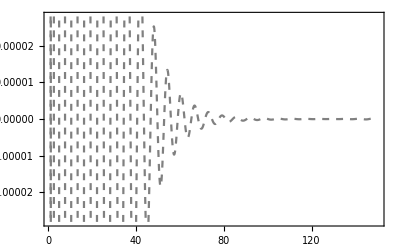

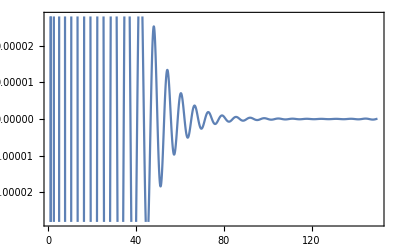

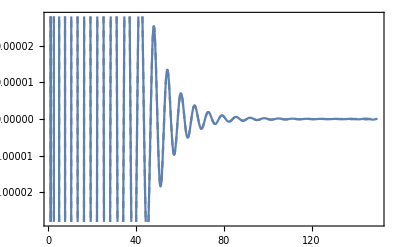

```mathematica
f[x_]=1-1/x;V[x_]=f[x]((l(l+1))/x^2+(1-s^2)/x^3);ω=ωr-ⅈ ωi;ωr=1;ωi=0.1;s=0;l=1;xi=1.00000001;xf=150;

h[x_]=ⅇ^(ⅈ ω (x+Log[x-1]));
g[x_]=ⅇ^(-ⅈ ω (x+Log[x-1]));

sol=NDSolve[{f[x]^2 Ψ''[x]+f[x] f'[x] Ψ'[x]+(ω^2-V[x])Ψ[x]==0,Ψ[xi]==h[xi],Ψ[xf]==g[xf]},Ψ,{x,xi,xf},MaxSteps->Infinity];
pa=Plot[{Evaluate[Re[Ψ[x]]]/.sol},{x,xi,xf},Frame->True,PlotStyle->{Gray,Dashed}]

sol2=NDSolve[{f[x]^2 Ψ''[x]+f[x] f'[x] Ψ'[x]+(ω^2-V[x])Ψ[x]==0,Ψ[xi]==h[xi],Ψ'[xf]==g'[xf]},Ψ,{x,xi,xf},MaxSteps->Infinity];
pb=Plot[{Evaluate[Re[Ψ[x]]]/.sol2},{x,xi,xf},Frame->True]

Show[pa,pb]
```

## Comparing r_* with r, Schwarzschild

InterpolatingFunction::dmval: Input value {-40.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

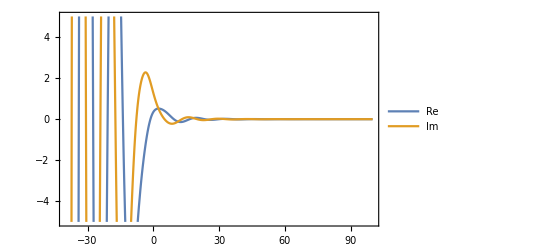

NDSolve::dsvar: «1» cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{((0.224122-0.0935543 ⅈ)+Times[«3»]) Ψ[InterpolatingFunction[«5»]]+Plus[«2»]^2 Ψ''[InterpolatingFunction[«5»]]==0,Ψ[2.0001]==ⅇ^(-0.0968048 InterpolatingFunction[«5»]) (Cos[Times[«2»]]+ⅈ Sin[«1»]),Ψ'[100]==0},Ψ,{InterpolatingFunction[{{2.0001,99.9901}},«3»,{Automatic}],2.0001,100},MaxSteps→∞,MaxStepFraction→0.001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: «1» cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{((0.224122-0.0935543 ⅈ)+Times[«3»]) Ψ[InterpolatingFunction[«5»]]+Plus[«2»]^2 Ψ''[InterpolatingFunction[«5»]]==0.,Ψ[2.0001]==2.71828^(-0.0968048 InterpolatingFunction[«5»]) (Cos[Times[«2»]]+(0.+1. ⅈ) Sin[«1»]),Ψ'[100.]==0.},Ψ,{«1»},MaxSteps→∞,MaxStepFraction→0.001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{((0.224122-0.0935543 ⅈ)+Times[«3»]) Ψ[InterpolatingFunction[«5»]]+Plus[«2»]^2 Ψ''[InterpolatingFunction[«5»]]==0,Ψ[2.0001]==ⅇ^(-0.0968048 InterpolatingFunction[«5»]) (Cos[Times[«2»]]+ⅈ Sin[«1»]),Ψ'[100]==0},Ψ,{InterpolatingFunction[{{2.0001,99.9901}},«3»,{Automatic}],2.0001,100},MaxSteps→∞,MaxStepFraction→0.001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: «1» cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

```mathematica
m=1;xistar=-40;xfstar=100;xi=2.0001 m;xf=100;
vlogk0=Table[
vk:=y/.FindRoot[x ==y + 2m Log[y/(2m) - 1], {y,2m+0.0001}];
{x,vk},{x,xi,xf,0.01}];
r=Interpolation[vlogk0];

l=2;β=1 - s^2;s=0;ω=ωr-ⅈ ωi;ωr=0.4832110283763369;ωi=0.09680484660403677;η=((l-1)(l+2))/2;
f[x_]=1 - (2m)/r[x];
V[x_]=f[x]((l(l+1))/r[x]^2+ (2m β)/r[x]^3);

vlogkv=Table[
vk:=N[V[x]];
{x,vk},{x,xistar,xfstar,0.01}];
Vf=Interpolation[%];

h[x_] =ⅇ^(-ωi r[x])(Cos[ωr r[x]]+ⅈ Sin[ωr r[x]]);

Solution=NDSolve[{ψ''[x] + (ω^2-Vf[x])ψ[x]== 0, ψ[xfstar]==h[xfstar],ψ'[xfstar]==h'[xfstar]},ψ,{x,xistar,xfstar},MaxSteps->Infinity,MaxStepFraction->0.001];
Plot[{Evaluate[Re[ψ[x]]/.Solution],Evaluate[Im[ψ[x]]/.Solution]},{x,xistar,xfstar},Frame->True,PlotLegends->{"Re","Im"},PlotRange->{{xistar,xfstar},{-5,5}}]

fr[r_]=1 - (2m)/r;
Vr[r_]=fr[r]((l(l+1))/r^2+ (2m β)/r^3);
hr[r_] =ⅇ^(-ωi r)(Cos[ωr r]+ⅈ Sin[ωr r]);

sol=NDSolve[{fr[r]^2 Ψ''[r]+fr[r] fr'[r] Ψ'[r]+(ω^2-Vr[r])Ψ[r]==0,Ψ[xi]==hr[xi],Ψ'[xf]==hr'[xf]},Ψ,{r,xi,xf},MaxSteps->Infinity,MaxStepFraction->0.001];
Plot[{Evaluate[Re[Ψ[r]]]/.sol},{r,xi,xf},Frame->True]
```